# Project report

## Set point misbehaviour: the causes

D Malan

Department of Chemistry
University of Pretoria

13 February 2020

## Introduction

A previous report (Temperature control: set points and times) detailed how variation in the set point causes variation in the temperature program. This behaviour has been analyzed and can be simply explained.

## Experimental

Set points and measured temperatures from a previous chromatogram (2020_02_11-120014.dat) was obtained:

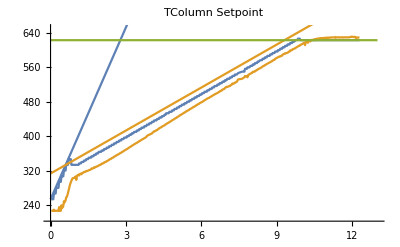

The blue dots represent the set points, and the orange dots the measured coaxial heater temperature. The straight lines shows the intended mathematical function.

The programmed rate was as follows:

```mathematica
TableForm[{{"",1,2,3},{"Rate (°C/min)",0,8000,2000},{"To temperature (°C)",-20,60,350},{"Hold time (s)",0,0,2}}]
```

| 1 | 2 | 3
Rate (°C/min) | 0 | 8000 | 2000
To temperature (°C) | -20 | 60 | 350
Hold time (s) | 0 | 0 | 2

The stationary points at 0.5 s and 10 that are visible in the figure above are the focus of the discussion.

The LabVIEW routine that calculates the set point was examined.

## Results

A GC temperature program is conventionally divided into a series of ramps and holds. During ramps the temperatures are increased at a constant rate, and during holds the temperature of the oven is held constant. Each hold or ramp is called a segment. In the table above Column 1 represents one segment (an initial hold of 0 s), and the other two columns each two segments, ramp (8000 and 2000) and a hold (0 s and 2 s).

It is assumed that the temperature of the column will closely follow the temperature of the oven, and hence of the set point. The figure shows that the coaxial heater does a good job of following the set point. There is a bit of a lag, but in general all the temperatures are covered, and the rate of change is close to the rate of change of the set point.

It should be noted that the high ramp rate at the beginning is not driven by the controller, but is caused by the coaxial heater taking on the temperature of the oven. The setpoint is changed at the given rate to mimic the behavior of the column. At higher temperatures the heater temperature is driven by resistive heating.

Three features of the temperature program are discussed in this report: The stationary point at the beginning of the temperature program and after the set point reversal at 0.5 s, the reversals at 0.5 s and 10 s, and the ramp retardation.

### Stationary points

The algorithm compares the current time with the start time of the segment. If the segment is a hold, and the current time has not yet exceeded the start time plus the hold time, then the set point is held constant. The problem with this approach is that if the hold time is zero, and the current time is the same as the start time of the segment, then the current time has not yet exceeded the start time plus the hold time, so the temperature setpoint is not changed. Because the control loop has a period of about 200 ms, this means that the set point will remain constant for 200 ms. Additionally, the set point of the hold time is also the set point of the start of the next ramp, so the set point is again held constant for another loop iteration, or about 200 ms.

The picture below is the voltage over the reference resistor, i.e. a measure of the power to the column:

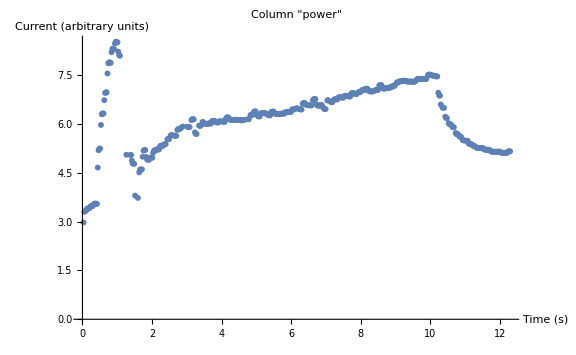

This shows that the power to the column is actually quite low at a time where the intention was that the power should be high to ensure a high ramp rate. Once the setpoint changes rapidly, the controller increases the power.

### Reversals

The intention was that the temperature constantly increase or stay constant, but the first figure above shows that at the end of each ramp the setpoint decreased before increasing again. Again, once the algorithm is properly understood the cause is clear. If the setpoint does not exceed the upper temperature of the segment, then a new setpoint is calculated by multiplying the ramp rate by the elapsed time. If it does exceed the set point, then proceed to the new segment. Every ramp segment is followed by a hold segment, but the hold segment inevitably has a lower set point than the end of the ramp, so the set point decreases. Additionally, as we saw in the previous paragraph, the set point is obliged to spend at least one loop iteration at this value. At the start of the next ramp, this is still the start value of the ramp, so another iteration is spent with the set point at this value.

### Ramp retardation

In the first figure above it can be see that the set point ramp is much later than intended, by one or two loop iterations. This is probably the main cause for the lack of repeatability in the chromatogram. This is caused by the way the algorithm handles the time. Each segment is given a start time, and this time is determined by the end of the previous segment. For example, during a hold, the hold segment is determined to have ended when the elapsed time exceeds the segment start time plus the hold time. This increments the state register and marks the next segment start time, so that during the next loop iteration the algorithm enters the ramp state. But this segment start time is by definition later than the previous segment’s start time plus the hold time, because the hold can only be judged as ended in the loop iteration after the iteration during which the hold time has actually elapsed. A similar argument holds for the end of ramps. A few events like these, and the start of the main ramp is easily retarded by a few loop iterations.

## Discussion

Because of a few approximations and simplifications, the algorithm used to set the setpoint causes differences between consecutive fast GC runs of tens or hundreds of milliseconds. This is intrinsic to the algorithm, and there are no errors in coding or faulty measurements involved.

It should be emphasized that there is nothing intrinsically wrong with this algorithm. For processes that have a loop rate of minutes, it will perform perfectly adequately. It is the mere fact that we are starting to need millisecond accuracy that it has become an issue.

Because it’s an algorithm, it can fairly easily be changed and the code modified. I believe that the first attempt at improvement should convert the current state-based approach to an algebraic approach. A given set of segments can be converted into a function that gives the desired temperature as a function of time. The input of the function would be the the elapsed time since the start of the temperature program. The output would be the desired temperature.

If these problems could be resolved, I believe the repeatability of the temperature set point ramp would be markedly improved. Power would be applied right from the start of the program, and there would be no stationary points or reversals. This would improve the chromatography: every stationary point is the equivalent of a cold spot on the column.

The study of this problem has reminded me again of how poorly time is managed in the whole SFC×GC LabVIEW program. Again, for many applications this would not matter, but for this one it does. So far I’ve discovered that LabVIEW has an implentation of FIFO buffers that is extremely fast. In future I would implement more of these. I think it is also possible to improve the temperature control by giving it it’s own control loop. I’ve done this with the pumps and the manifold controllers, but they were less intertwined with the other control issues.

The previous report blamed non-deterministic timing and the PID algorithm for the repeatability issues. The discovery of the set point problems described here removes some of the blame, but not all of it: more repeatable timing and fewer lost data points might have hidden these issues for much longer. There is plenty of evidence that lost data points also affect the temperature ramps.

## Conclusion

The temperature set point algorithm is not suitable for fast temperature programmed gas chromatography, but its shortcomings are clear and it can be replaced.

## Recommendations

Write a mathematical function to calculate the set point based on the elapsed time.

Switch to a real-time operating system with deterministic timing.

Use some kind of master clock to determine the execution of the program.

Use more FIFOs.

Give the temperature control system its own control loop.